```mathematica
(* Cross-validation checks. *)
base=DirectoryName[NotebookFileName[]]<>"../";
```

```mathematica
(* Load / add data files *)
bubblesScaled =Table[Import[base<>"csv/bubbleScaled-"<>ToString[i]<>".tsv", HeaderLines-> 1], {i, 1,2}];
```

```mathematica
(* 1.b Set up cross validation loop: *)
bandwidthSeq=Range[3, 20, 1]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
k=10;
```

```mathematica
folds = RandomChoice[Range[k], Length[#]]&/@bubblesScaled;
```

```mathematica
cvErrorMtrx = ConstantArray["NA", {Length[bandwidthSeq], k}];
cvErrorMtrx//MatrixForm
```

(NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA)

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
(* Processing only for 2nd bubble: *)
bubble=2;
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
maxDist=Max[bubbleScaled[[All, 1]]]-Min[bubbleScaled[[All, 1]]]
```

1.00114

```mathematica
(* 1.c Nested for loop for bandwidth cross-validation. Slow (shortcut below) *)
Monitor[For[i=1,i<=Length[bandwidthSeq],i++,{For[j=1, j<= k, j++,{
fit =bubbleScaled[[Select[Range[Length[bubbleScaled]], folds[[bubble]][[#]]!= j&]]];
pred=bubbleScaled[[Select[Range[Length[bubbleScaled]], folds[[bubble]][[#]]== j&]]];
	preds = LoessR[fit, Scaled[bandwidthSeq[[i]]/Length[bubbleScaled]], pred[[All, 1]], {InterpolationOrder-> 2,"WeightsFunction"-> ((1-(Norm[#]/maxDist)^3)^3&) }];
cvErrorMtrx[[i]][[j]]=Mean[(pred[[All, 2]]-preds)^2];
}]}],{i,j}]
```

```mathematica
(* 4. Calculate cross-validation mean square error for each fold: *)
cvErrors=Map[Mean, cvErrorMtrx]
```

{0.0000436787,0.0000342659,0.0000342263,0.0000346442,0.0000358173,0.0000371721,0.0000388166,0.0000394488,0.0000403044,0.0000418349,0.0000436795,0.0000451223,0.0000472776,0.0000488244,0.0000505534,0.0000524178,0.0000537083,0.0000549314}

```mathematica
bestIndex=SortBy[Table[{i, cvErrors[[i]]},{i, 1, Length[cvErrors]}], Last][[1]][[1]]
```

3

```mathematica
bestBandwidth=bandwidthSeq[[bestIndex]]
```

5

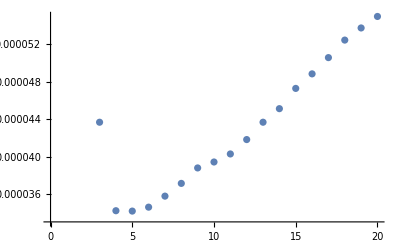

```mathematica
(* Plot results: *)
ListPlot[MapThread[{#1, #2}&, {bandwidthSeq, cvErrors}]]
```